## Governing ODE and BCs for static landslide on non-planar base

The above ODE describes static equilibrium for a landslide with frictional boundary conditions.

### Model Parameters

```mathematica
θv = π/4;
fv =1.0*Tan[θv];(*Assume friction coefficient matches average orientation*)
(*fv=0.5;*)
bmax = 0.1;
Nsin = 0.15;(*number of sine cycles*)
H0 = 0.20;(*Boundary condition for H*)
ρ = 0.1;(*ratio of ice/rock density*)
(*Multiplier to compare ice with no-ice case*)
γ = 1.0;
(*bv = bmax*Sin[ Nsin *π x];*)
bv = -bmax*Exp[-(x/(2 Nsin))^2];
(*bv =4 bmax*(x^2+x);(* quadratic basal topography*)*)
eqnODE = -D[H[x],x] - 0.5*(Tan[θv]-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*H[x] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv]);
solss = NDSolve[{
eqnODE,H[-1]==H0*γ,WhenEvent[H[x]==0,{xend=x,"StopIntegration"}]
},H,{x,-1,0}];
(*Plot[{H[x]/.solss,bv},{x,-1,xend},PlotRange->{{-1,0},{-0.2,H0}}]*)
(*h = bv+ H[x]/. solss;*)
```

## Instead of simply integrating , let us log-transform to such that the solution is strictly positive

```mathematica
eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*(Tan[θv]-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*Exp[ϕ[x]] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv]);
sollogss = NDSolve[{eqnlogODE,ϕ[-1]==Log[H0*γ]},ϕ,{x,-1,0}];
H2 =  Exp[ϕ[x]/.sollogss];
h = bv+ H2;
(*NIntegrate[H2,{x,-1,0}]*)
```

## Plot results

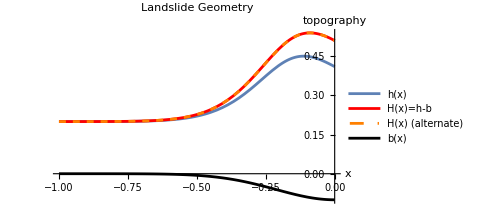

```mathematica
p1=Plot[{h,H2,H[x]/. solss,bv},{x,-1,0},PlotStyle->{DarkBlue,{Red,Thick},{Orange,Dashed},Black},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","H(x) (alternate)","b(x)"},ImageSize->Medium,PlotRange->Full]
```

## Incorporate ice barrier to non-planar landslide geometry

The ODE describes the force balance for a landslide under gravity being buttressed by a glacier

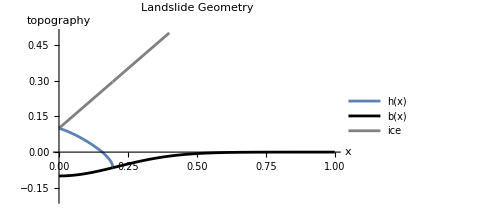

```mathematica
θi = θv;(*glacier geometry*)
(*bvi = bmax*Sin[ Nsin*π (x-1)];*)
bvi = bv;
(*H=h-b boundary condition*)
HBC = H0;
hg = HBC+(bvi/.x->0);
xendice=1.0;
eqiceODE = (ρ-1)(D[H[x],x]+D[bvi,x]) - 0.5*((Tan[θv]-D[bvi,x])/(1+(D[bvi,x])^2)*D[bvi,x,x]/(1+D[bvi,x]*Tan[θv]))*H[x]  -ρ*(hg - H[x]-bvi + x*Tan[θi])*(fv/H[x]+D[bvi,x,x]*(Tan[θv]/(1+D[bvi,x]*Tan[θv])-D[bvi,x]/ (1+(D[bvi,x])^2)))==fv + ρ *Tan[θv]-(Tan[θv]-D[bvi,x])/(1+D[bvi,x]*Tan[θv]);
solice = NDSolve[{eqiceODE,H[0]==HBC,WhenEvent[H[x]<=0.0000001,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
(*thickness has artifacts*)
Hsol= H[x]/.solice;
Hice[x_]:=Piecewise[{{Evaluate[Hsol],0<=x<=xendice }},0]
hice[x_] := bvi+ Hice[x];
(*Plot[{Hice[x],hice[x]},{x,0,1}]*)
(*Translate ice-free solution to new coordinates*)
(*hsol[x_]:=Evaluate[h];
hshift[x_]:=hsol[x-1];*)
p2=Plot[{hice[x],bvi,hg+x*Tan[θi]},{x,0,1},PlotStyle->{DarkBlue,Black,Gray},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","b(x)","ice"},ImageSize->Medium,PlotRange->{-0.2,0.5}]
```

## Now solve for ice+no-ice landslide

The ice-case is already solved for , so now we just need to solve for the no-ice section of the landslide

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-5.08145×10^6] is too small to represent as a normalized machine number; precision may be lost.

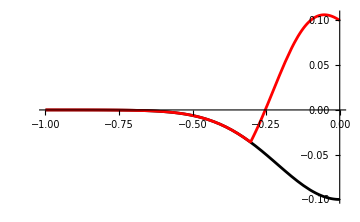

```mathematica
(*bv = bmax*Sin[ Nsin*π (x-1)];*)
eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*(Tan[θv]-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*Exp[ϕ[x]] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv]);
xend=-1.0;
sollogss = NDSolve[{eqnlogODE,ϕ[0]==Log[HBC],WhenEvent[ϕ[x]<=-6,{xend=x,"StopIntegration"}]},ϕ,{x,-1,0}];
(*Extract height for no-ice and with ice case*)
H2 =  Exp[ϕ[x]/.sollogss];
h = bv+ H2;
Plot[{bv,h},{x,-1,0},PlotStyle->{Black,Red},ImageSize->Medium,PlotRange->All]
```

## Compute area under landslide and find equivalent BC for ice-free landslide

{0.0657888}

{0.925,0.0669817}

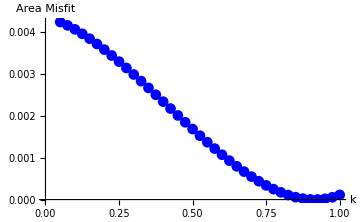

```mathematica
Harea=NIntegrate[Hsol,{x,0,Min[xendice,1.0]}]+NIntegrate[H2,{x,Max[xend,-1],0}]
ComputeArea[k_?NumericQ]:=Quiet@Module[{soltest,ϕfun,ϕval,xmin,xmax},soltest=NDSolve[{eqnlogODE,ϕ[0]==Log[HBC*k]},ϕ,{x,-1.0,1.0}];
ϕfun=ϕ/. soltest[[1]];
{xmin,xmax}=First[ϕfun[[1]]];
ϕval[x_]:=Exp[ϕfun[x]];
NIntegrate[ϕval[x],{x,Max[xmin,-1.0],Min[xmax,1.0]}]]
results=ParallelTable[{k,ComputeArea[k]},{k,0.05,1,0.025}];
misfit=(results[[All,2]]-Harea[[1]])^2;
minIndex=First@Ordering[misfit,1];
results[[minIndex,All]]
ListLinePlot[Transpose[{results[[All,1]],misfit}],AxesLabel->{"k","Area Misfit"},PlotMarkers->Automatic,PlotStyle->Blue,ImageSize->Medium]
(*kval=FindMinimum[{(ComputeArea[k]-Harea)^2,0<=k<=0.8},{k,0.5}];*)
```

NDSolve::ndsz: At x == -0.284026, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 0.305496, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-5.08145×10^6] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-4.64477×10^39] is too small to represent as a normalized machine number; precision may be lost.

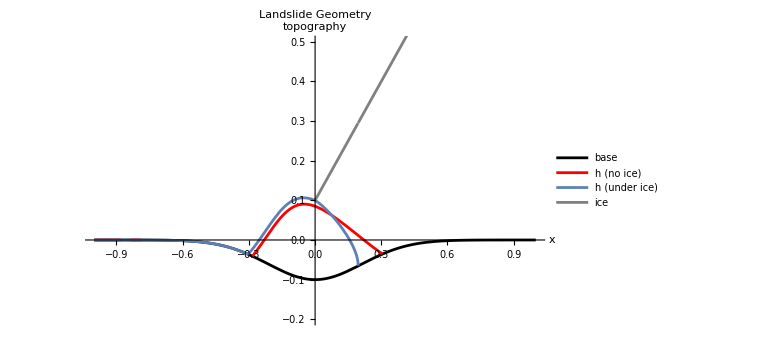

```mathematica
(*Solve for situation with no ice at all*)
kval=results[[minIndex,1]];
(*kval=0.7;*)
solnoice = NDSolve[{eqnlogODE,ϕ[0]==Log[HBC*kval]},ϕ,{x,-1.0,1.0}];
Hnoice =  Exp[ϕ[x]/.solnoice];
hnoice= bv+ Hnoice;
p1=Plot[{hice[x],hg+x*Tan[θi]},{x,0,1},PlotStyle->{DarkBlue,{Gray,Thick}},PlotLegends->{"h (under ice)", "ice"}];
p2=Plot[h,{x,-1,0},PlotStyle->DarkBlue];
p3=Plot[{bvi,hnoice},{x,-1,1.0},PlotStyle->{Black,Red},PlotLegends->{"base","h (no ice)"}];
Show[p3,p1,p2,PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},ImageSize->Large,PlotRange->{-0.2,0.5},PlotLegends->All]
(*p2=Plot[{hice[x],h,bvi,hg+x*Tan[θi]},{x,-1,1},PlotStyle->{DarkBlue,Red,Black,{Gray,Dashed}},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h (under ice)","h (no ice)","b(x)","ice"},ImageSize->Large,PlotRange->{-0.2,0.75}]*)
```

Compare area under the curves for landslide under ice with no-ice

```mathematica
NIntegrate[Hsol,{x,0,xendice}]+NIntegrate[H2,{x,xend,0}]
Hfun=ϕ/. solnoice[[1]];
{xmin,xmax}=First[Hfun[[1]]];
NIntegrate[Hnoice,{x,xmin,xmax}]
```

{0.0657888}

{0.0669817}